# Dynamics of Multi-Spring Systems

## Jack McArthur

Obtaining an analytical solution to the three spring system using the Laplace transform.

```mathematica
threesprings={
x1''[t]== -k1 x1[t]+k2(x2[t]-x1[t]),
x2''[t]== -k2(x2[t]-x1[t])+k3(x3[t]-x2[t]),
x3''[t]== -k3(x3[t]-x2[t])+DiracDelta[t]
};
initialconds={x1[0]-> 0,x1'[0]->0,x2[0]->0,x2'[0]->0,x3[0]->0,x3'[0]->0};

soln1=First@Solve[LaplaceTransform[threesprings,t,s]/.initialconds,LaplaceTransform[{x1[t],x2[t],x3[t]},t,s]];
solnInv1=InverseLaplaceTransform[soln1,s,t];
```

Taking the real part of the obtained solutions and lowering precision to obtain well-behaved solutions for x1[t], x2[t], and x3[t]. The graphs below are a “before and after” representation.

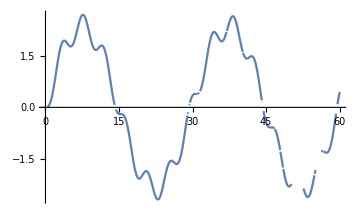
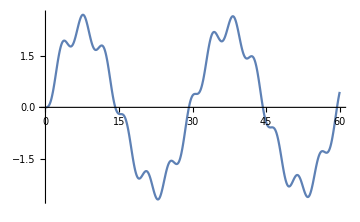

```mathematica
(*this function ignores the imaginary components of the motion plots; very important to get rid of complex infinity results and holes in the graph.*)
realify[f_,rule_,t_]:=Chop[Simplify[Re[ComplexExpand[f[t]/.rule]],Element[{t},Reals]]];

x2rule=solnInv1[[2]]/.{k1->1.,k2->0.1,k3->1.};
realify[x2,x2rule,t];
Row[{Plot[x2[t]/.x2rule,{t,0,60},ImageSize->Medium],(*not realified, holes*)
Plot[realify[x2,x2rule,t],{t,0,60},ImageSize->Medium](*realified, no holes*)}]
```

Plotting the displacements of the three springs over time:

```mathematica
Manipulate[Module[{x2soln,x1soln,x3soln,motion},
motion=solnInv1/.{k1->k1v,k2->k2v,k3->k3v};
x1soln=motion[[1]];
x2soln=motion[[2]];
x3soln=motion[[3]];
Plot[{realify[x1,x1soln,t],
realify[x2,x2soln,t],
realify[x3,x3soln,t]},
{t,0,50},PlotStyle-> {Red,Blue,Green}]],
{{k1v,0.5,"k spring 1"},0.5,3.,0.5,Appearance->"Labeled"}, 
{{k2v,0.5,"k spring 2"},0.5,3.,0.5,Appearance->"Labeled"},
{{k3v,0.5,"k spring 3"},0.5,3.,0.5,Appearance->"Labeled"}]
```

Creating a manipulable simulation of the three displacements, as well as a preloaded animation for one possible set of values of k that runs much smoother.

```mathematica
spring[r_:{1,0},l_:{0,0},n_:20,w_:1]:=
If[r==l,Return[Line[{{0,-w}+l,{0,w}+l}]],
Return[Line@Transpose[{r-l,-Cross[r-l]}.{(#-1)/(2n),Re[I^#]w/Norm[r-l]}+l]]&@Range[2n+1];]
```

```mathematica
Manipulate[
motion=solnInv1/.{k1->k1v,k2->k2v,k3->k3v};
x1soln=realify[x1,motion[[1]],t];
x2soln=realify[x2,motion[[2]],t];
x3soln=realify[x3,motion[[3]],t];

disp1={x1soln/.t->tv,0};
disp2={x2soln/.t-> tv,0};
disp3={x3soln/.t-> tv,0};

Graphics[
{Rectangle[{-0.02,-0.3},{0.02,0.3}],
Red,spring[disp1,{0.,0.},6,0.5],
Red,PointSize[0.03],Point[disp1],
Blue,spring[disp2,disp1,6,0.5],
Blue,PointSize[0.03],Point[disp2],
Green,spring[disp3,disp2,6,0.5],
Green,PointSize[0.03],Point[disp3]},
ImageSize->{400,250},
PlotRange->{{-2.,2},{-1.25,1.25}}],

{{k1v,0.5,"k spring 1"},0.5,3.,0.5,Appearance->"Labeled"}, 
{{k2v,0.5,"k spring 2"},0.5,3.,0.5,Appearance->"Labeled"},
{{k3v,0.5,"k spring 2"},0.5,3.,0.5,Appearance->"Labeled"},
{{tv,0,"time elapsed"},0.,20.,0.1,AnimationRate->2,Appearance->"Open"}
]
```

Preset animation (k_1 = 0.5 , k_2 = 0.5, k_3 = 1):

```mathematica
anmotion=solnInv1/.{k1->0.5,k2->0.5,k3->1};
x1sol=realify[x1,anmotion[[1]],t];
x2sol=realify[x2,anmotion[[2]],t];
x3sol=realify[x3,anmotion[[3]],t];

dis1={x1sol/.t->tv,0};
dis2={x2sol/.t-> tv,0};
dis3={x3sol/.t-> tv,0};

ListAnimate[Table[
Graphics[
{Rectangle[{-0.02,-0.3},{0.02,0.3}],
Red,spring[dis1,{0.,0.},6,0.5],
Red,PointSize[0.03],Point[dis1],
Blue,spring[dis2,dis1,6,0.5],
Blue,PointSize[0.03],Point[dis2],
Green,spring[dis3,dis2,6,0.5],
Green,PointSize[0.03],Point[dis3]},
ImageSize->{400,250},
PlotRange->{{-2.,2},{-1.25,1.25}}],{tv,0,20,0.1}]]
```

Generalization to n springs: the function below returns the ODE governing the nth spring in a system in terms of the forces caused by the one or two springs on either side of it and any external forces.

```mathematica
Subscript[x,0][t]=0;

nthspring[x_,n_?IntegerQ,nmax_?IntegerQ]:=
Module[{leftspring,rightspring},
leftspring[n,t_]:=Subscript[k,n]*(Subscript[x,n][t]-Subscript[x,n-1][t]);
rightspring[n,t_]:=Subscript[k,n+1]*(Subscript[x,n+1][t]-Subscript[x,n][t]);

leftspring[0,t]=0;
rightspring[nmax,t]=0;

D[Subscript[x,n][t],{t,2}]+ leftspring[n,t]- rightspring[n,t]==Subscript[f,n][t]
]
```

Defining a set of ODEs and initial conditions (every mass starts at x = 0) for the n = 10 springs case. This includes the initial force on the 10th spring, and a spring constants of 0.5 for all springs.

```mathematica
springnum=10;

odes=Table[nthspring[x,i,springnum]/.
{Subscript[f,i][t]-> If[i==springnum,Exp[-100t^2]/(Sqrt[π]/20),0],
Subscript[k,_]-> 0.5},
{i,1,springnum}];
odes//TableForm (*lists the ODEs in a legible format*)
ics=Join[Table[Subscript[x,i][0]== 0,{i,1,springnum}],Table[Subscript[x,i]'[0]== 0,{i,1,springnum}]];
vars=Table[Subscript[x,i][t],{i,1,springnum}];
```

0.5 x_1[t]-0.5 (-x_1[t]+x_2[t])+x_1''[t]==0
0.5 (-x_1[t]+x_2[t])-0.5 (-x_2[t]+x_3[t])+x_2''[t]==0
0.5 (-x_2[t]+x_3[t])-0.5 (-x_3[t]+x_4[t])+x_3''[t]==0
0.5 (-x_3[t]+x_4[t])-0.5 (-x_4[t]+x_5[t])+x_4''[t]==0
0.5 (-x_4[t]+x_5[t])-0.5 (-x_5[t]+x_6[t])+x_5''[t]==0
0.5 (-x_5[t]+x_6[t])-0.5 (-x_6[t]+x_7[t])+x_6''[t]==0
0.5 (-x_6[t]+x_7[t])-0.5 (-x_7[t]+x_8[t])+x_7''[t]==0
0.5 (-x_7[t]+x_8[t])-0.5 (-x_8[t]+x_9[t])+x_8''[t]==0
0.5 (-x_8[t]+x_9[t])-0.5 (-x_9[t]+x_10[t])+x_9''[t]==0
0.5 (-x_9[t]+x_10[t])+x_10''[t]==(20 ⅇ^(-100 t^2))/(√π)

Obtaining the solution for the set of ODEs numerically and plotting/animating the displacements over time for each of the ten springs, distinguished by hue for illustrative and fun purposes. Surprisingly, this is faster than the analytical solution for three springs above.

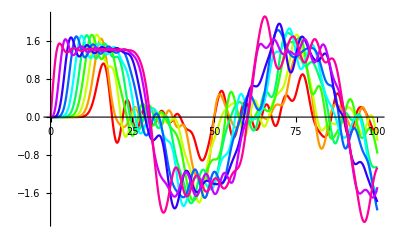

```mathematica
solnset=First@NDSolve[Join[odes,ics],vars,{t,0,100}];

tensprings=Table[Subscript[x, i][t]/.solnset[[i]],{i,1,springnum}];
displacements=Join[{0},tensprings];Plot[Evaluate[tensprings],{t,0,100},PlotStyle-> Table[Hue[(j-1)/10.],{j,1,10}]]
```

```mathematica
Clear[i,t,tv]

ListAnimate[Table[
Show[
Graphics[
Rectangle[{-0.02,-0.3},{0.02,0.3}]],
Graphics[
Table[{Hue[(i-1)/springnum],
spring[{Indexed[displacements,i+1]/.t->tv,0.},{displacements[[i]]/.t->tv,0.},6,0.5],
PointSize[0.03],Point[{Indexed[displacements,i+1]/.t->tv,0.}]},
{i,1,springnum}]],
ImageSize->{500,250},
PlotRange->{{-2.5,2.5},{-1.25,1.25}}],{tv,0,100,0.2}]]
```